```mathematica
SetOptions[EvaluationNotebook[],PrintPrecision->Round[MachinePrecision]]
```

## Import Data

```mathematica
xdata={20,40,60,80,100,120,140,160,180,200};
ydata={33,30,27,26,23,20,19,17,18,12};
```

```mathematica
(*xdata={20,40,60,80,100,120,140,160,180,200};
ydata={36,33,30,28,25,22,21,19,19,13};*)
```

```mathematica
Length/@{xdata,ydata}
```

{10,10}

```mathematica
dy=Sqrt/@ydata//N
```

{6.,5.74456,5.47723,5.2915,5.,4.69042,4.58258,4.3589,4.3589,3.60555}

```mathematica
n=Length[xdata]
```

10

## Creating Table

```mathematica
Transpose[{xdata,ydata,Round[dy,0.1]}]//TeXForm//CopyToClipboard
```

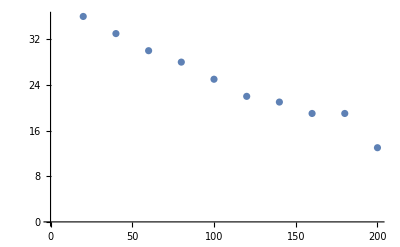

```mathematica
ListPlot[Transpose[{xdata,ydata}]]
```

```mathematica
logy=Log/@ydata//N
```

{3.58352,3.49651,3.4012,3.3322,3.21888,3.09104,3.04452,2.94444,2.94444,2.56495}

```mathematica
dlogy=Table[dy[[i]]/ydata[[i]],{i,1,Length[ydata]}]
```

{0.166667,0.174078,0.182574,0.188982,0.2,0.213201,0.218218,0.229416,0.229416,0.27735}

```mathematica
Table[Log[Around[ydata[[i]],dy[[i]]]],{i,1,Length[ydata]}]
```

{3.580.17,3.500.17,3.400.18,3.330.19,3.220.20,3.090.21,3.040.22,2.940.23,2.940.23,2.560.28}

```mathematica
Transpose[{xdata,Round[logy,0.01],Round[dlogy,0.01]}]//TeXForm//CopyToClipboard
```

## Unweighted Linear Regression

```mathematica
sumxv1=Total[xdata]
sumyv1=Total[logy]
sumx2v1=Total[#^2&/@xdata]
sumxyv1=Sum[xdata[[i]]logy[[i]],{i,1,Length[xdata]}]
```

1100

31.6217

154000

3315.32

```mathematica
Δv1=n(sumx2v1)-(sumxv1)^2
```

330000

```mathematica
a1=(sumx2v1 sumyv1-sumxv1 sumxyv1)/Δv1
```

3.70571

```mathematica
b1=1/Δv1 (n sumxyv1 - sumxv1 sumyv1)
```

-0.0049413

```mathematica
LinearModelFit[Transpose[{xdata,logy}],x,x]
```

FittedModel[3.70571-0.0049413 x]

```mathematica
s2=Sum[(logy[[i]]-a1 - b1 xdata[[i]])^2 / (n - 2),{i,1,Length[logy]}]
```

0.00540282

```mathematica
√((s2 sumx2v1)/Δv1)
```

0.0502127

```mathematica
Sqrt[n s2/Δv1]
```

0.000404626

```mathematica
-Log[2]/b1//N
```

140.276

```mathematica
(Log[2]/b1^2)√((n s2)/Δv1)
```

11.4867

## Weighted Linear Regression

```mathematica
Δv2=Total[1/#^2&/@ dlogy]Sum[xdata[[i]]^2/dlogy[[i]]^2,{i,1,Length[xdata]}]-(Sum[xdata[[i]]/dlogy[[i]]^2,{i,1,Length[xdata]}])^2
```

1.87712×10^8

```mathematica
a2=1/Δv2 (Sum[logy[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}] Sum[xdata[[i]]^2/dlogy[[i]]^2,{i,1,Length[logy]}]-Sum[xdata[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}]Sum[xdata[[i]]logy[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}])
```

3.69087

```mathematica
b2=1/Δv2(Total[1/#^2&/@ dlogy]Sum[xdata[[i]]logy[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}]-Sum[xdata[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}]Sum[logy[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}])
```

-0.00476232

```mathematica
Sqrt[1/Δv2 Sum[xdata[[i]]^2/dlogy[[i]]^2,{i,1,Length[logy]}]]
```

0.125464

```mathematica
db2=Sqrt[1/Δv2 Total[1/#^2&/@ dlogy]]
```

0.00114478

```mathematica
-Log[2]/b2
```

145.548

```mathematica
Log[2]/b2^2 db2
```

34.9872

## Poisson Regression

```mathematica
eq1=(∑_(i=1)^Length[xdata] logy⟦i⟧/(a+b xdata⟦i⟧))-n==0
eq2=∑_(i=1)^Length[xdata] (logy⟦i⟧ xdata⟦i⟧)/(a+b xdata⟦i⟧)-∑_(i=1)^Length[xdata] xdata⟦i⟧==0
```

-10+3.58352/(a+20 b)+3.49651/(a+40 b)+3.4012/(a+60 b)+3.3322/(a+80 b)+3.21888/(a+100 b)+3.09104/(a+120 b)+3.04452/(a+140 b)+2.94444/(a+160 b)+2.94444/(a+180 b)+2.56495/(a+200 b)==0

-1100+71.6704/(a+20 b)+139.86/(a+40 b)+204.072/(a+60 b)+266.576/(a+80 b)+321.888/(a+100 b)+370.925/(a+120 b)+426.233/(a+140 b)+471.11/(a+160 b)+529.999/(a+180 b)+512.99/(a+200 b)==0

```mathematica
{a3,b3}=Values@FindRoot[Evaluate[{(∑_(i=1)^Length[xdata] logy⟦i⟧/(a+b xdata⟦i⟧))-n,∑_(i=1)^Length[xdata] (logy⟦i⟧ xdata⟦i⟧)/(a+b xdata⟦i⟧)-∑_(i=1)^Length[xdata] xdata⟦i⟧}],{{a,a1},{b,b1}},Method->"Newton"]
```

{3.71007,-0.00498096}

```mathematica
monitoredFindRoot[args__]:=Module[{s=0,e=0,j=0},{FindRoot[args,StepMonitor:>s++,EvaluationMonitor:>e++,Jacobian->{Automatic,EvaluationMonitor:>j++}],"Steps"->s,"Evaluations"->e,"Jacobian Evaluations"->j}]
```

```mathematica
monitoredFindRoot[Evaluate[{(∑_(i=1)^Length[xdata] logy⟦i⟧/(a+b xdata⟦i⟧))-n,∑_(i=1)^Length[xdata] (logy⟦i⟧ xdata⟦i⟧)/(a+b xdata⟦i⟧)-∑_(i=1)^Length[xdata] xdata⟦i⟧}],{{a,a1},{b,b1}}]
```

{{a→3.71007,b→-0.00498096},Steps→3,Evaluations→4,Jacobian Evaluations→3}

```mathematica
(∑_(i=1)^Length[xdata] logy⟦i⟧/(a3+b3 xdata⟦i⟧))-n
∑_(i=1)^Length[xdata] (logy⟦i⟧ xdata⟦i⟧)/(a3+b3 xdata⟦i⟧)-∑_(i=1)^Length[xdata] xdata⟦i⟧
```

0.

-2.27374×10^-13

```mathematica
eq1[[1]]/.sol[[2]]
```

0.272859

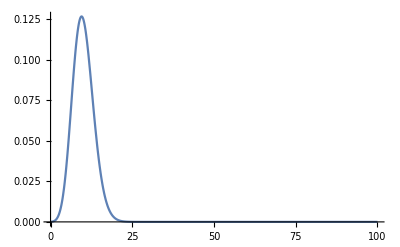

```mathematica
Plot[PDF[PoissonDistribution[10]][x],{x,0,100},PlotRange->All]
```

```mathematica
-Log[2]/b3
```

139.159

```mathematica
Log[2]/b3^2 db2
```

31.9831

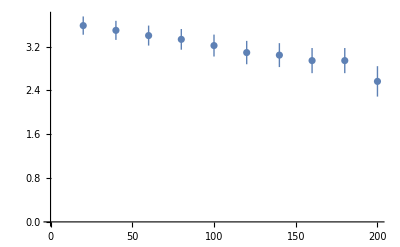

```mathematica
ListPlot[Transpose[{xdata,Table[Around[logy[[i]],dlogy[[i]]],{i,1,Length[logy]}]}],PlotRange->All,AxesOrigin->{0,0}]
```